```mathematica
Clear["Global`*"]
L=10;
```

```mathematica
ℏ=1;
m=1;
k=1;
ω=√(k/m);
infsqrE[n_]=1/(2 m) ((n π)/(2 L ℏ))^2//N;
λ=0;
v[x_]:=0(*1/2 m ω^2 x^2*)(*+λ x^4*)
(*Plot[v[x],{x,-L,L},AxesStyle->AbsoluteThickness[1],AxesLabel->{"x","V(x)"}]*)
```

```mathematica
infsqrE[1]
```

0.012337

```mathematica
TISE[ϵ_]:=-ℏ^2/(2 m)ψ''[x]+(ϵ-v[x]) ψ[x]
bcs={ψ[-L]==0,ψ'[-L]==0.0001};
```

```mathematica
wavefunc[ϵ_]:=NDSolve[{TISE[ϵ]==0,bcs},ψ,{x,-L,L}]
DSolve[{TISE[ϵ]==0,bcs},ψ,{x,-L,L}]
```

{{ψ→Function[{x},(ⅇ^(-1.41421 (10.+1. x) √ϵ) (-0.0000353553+0.0000353553 ⅇ^((28.2843+2.82843 x) √ϵ)))/(√ϵ)]}}

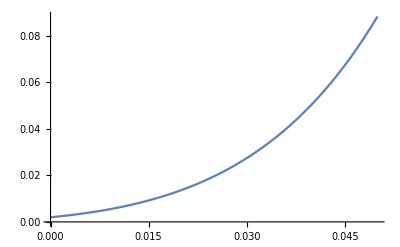

```mathematica
soln[x_?NumericQ,ϵ_?NumericQ]:=ψ[x]/.wavefunc[ϵ][[1]]
Plot[soln[L,ϵ],{ϵ,0,0.05}]
```

```mathematica
eval=ϵ/.FindRoot[soln[L,ϵ],{ϵ,0,0.7}]
(*efunc[x_]=ψ[x]/.wavefunc[eval][[1]];*)
```

0.0451187

```mathematica
ψnn[x_]:=efunc[-x]/;x>0;
normconst=Sqrt[NIntegrate[ψnn[x]^2,{x,-L,L}]];
ψ[x_]:=ψnn[x]/normconst;
```

NIntegrate::inumr: The integrand ψnn[x]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-20,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Plot[ψ[x],{x,-L,L},AxesLabel->{"x","ψ"},PlotRange->{0,1}];
```

NIntegrate::inumr: The integrand ψnn[x]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-20,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.